还有什么我们尚未论及

Wolfram 语言的内容比我们在本书中所涉及的要多得多。以下是我们所遗漏的众多主题和领域中的一部分。

#### 构建用户界面

创建一个标签式界面：

```mathematica
TabView[Table[ListPlot[Range[20]^n],{n,5}]]
```

12345

用户界面只是另一种类型的符号表达式；创建一个由滑块组成的网格：

```mathematica
Grid[Table[Slider[ ],4,3]]
```

|  | 
 |  | 
 |  | 
 |  |

#### 函数可视化

绘制一个函数：

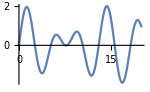

```mathematica
Plot[Sin[x]+Sin[Sqrt[2] x],{x,0,20}]
```

三维等高线图：

```mathematica
ContourPlot3D[x^3+y^2-z^2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

#### 数学计算

进行符号计算，其中 x 为代数变量：

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

计算方程的符号解：

```mathematica
Solve[x^3-2x+1==0,x]
```

{{x→1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

符号化地计算微积分：

```mathematica
Integrate[Sqrt[x+Sqrt[x]],x]
```

1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

以传统的数学形式显示结果：

```mathematica
Integrate[AiryAi[x],x]//TraditionalForm
```

-(x (3^(1/3) x (2/3)^2 _1 F_2(2/3;4/3,5/3;x^3/9)-3 1/3 5/3 _1 F_2(1/3;2/3,4/3;x^3/9)))/(9 3^(2/3) 2/3 4/3 5/3)

使用二维符号进行输入：

```mathematica
∑_(i=0)^n (Binomial[n,i] i!)/((n+1+i)!)
```

(√π)/(2 (1/2 (1+2 n))!)

#### 数值计算

在一个球的范围内求函数的最小值：

```mathematica
NMinimize[{x^4+y^4-z/(x+1),y>0},{x,y,z}∈Ball[ ]]
```

{-7.34516,{x→-0.971029,y→0.0139884,z→0.238555}}

求解一个微分方程，以得到一个近似的函数：

```mathematica
NDSolve[{y''[x]+ Sin[y[x]]y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

使用近似函数来绘图：

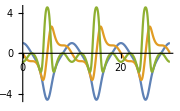

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.%],{x,0,30}]
```

#### 几何体

半径为 r 的圆盘的面积：

```mathematica
Area[Disk[{0,0},r]]
```

π r^2

通过“收缩包裹”在 3D 中的 100 个随机点来创建一个形状：

```mathematica
ConvexHullMesh[RandomReal[1,{100,3}]]
```

-Graphics-

#### 算法

找到游历欧洲各国首都的最短路线(旅行推销员问题)。

```mathematica
With[{c=LinguisticAssistant},GeoListPlot[c[[Last@FindShortestTour[c]]],Joined->True]]
```

-Graphics-

对一个很大的数字进行因式分解：

```mathematica
FactorInteger[2^255-1]
```

{{7,1},{31,1},{103,1},{151,1},{2143,1},{11119,1},{106591,1},{131071,1},{949111,1},{9520972806333758431,1},{5702451577639775545838643151,1}}

#### 逻辑学

创建一个真值表：

```mathematica
BooleanTable[p||q&&(p||!q),{p},{q}]//Grid
```

True | True
False | False

找到一个布尔函数的最小表示：

```mathematica
BooleanMinimize[BooleanCountingFunction[{2,3},{a,b,c,d}]]//TraditionalForm
```

(a∧b∧¬d)∨(a∧¬b∧c)∨(a∧¬c∧d)∨(¬a∧b∧d)∨(b∧c∧¬d)∨(¬b∧c∧d)

#### The Computational Universe

运行我最喜欢的例子，一个非常简单的程序，但是其行为非常复杂：

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},200]]
```

-Graphics-

RulePlot 可以显示其底层规则：

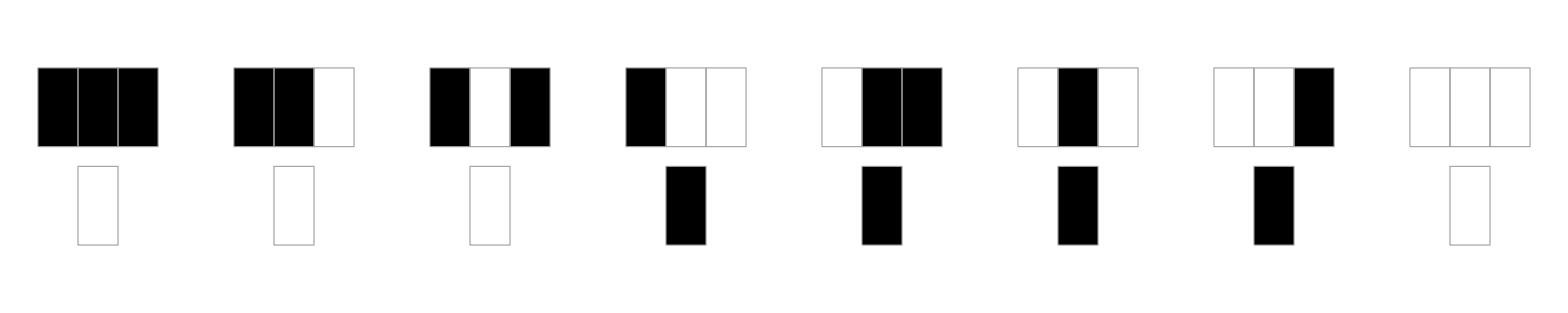

```mathematica
RulePlot[CellularAutomaton[30]]
```

#### 构建 API

部署一个简单的网络 API，用于找出与指定地点的距离：

```mathematica
CloudDeploy[APIFunction[{"loc" -> "Location"}, GeoDistance[#loc, Here] &]]
```

CloudObject[]

为外部 Java 程序创建可嵌入的代码，以调用 API：

```mathematica
EmbedCode[%,"Java"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Java:
Code
 | Copy to Clipboard
import java.net.URL;
import java.net.HttpURLConnection;
import java.net.URLEncoder;
import java.io.InputStream;
import java.io.BufferedReader;
import java.io.InputStreamReader;
import java.io.DataOutputStream;
import java.io.IOException;

public class WolframCloudCall {

    public static String call(String loc) throws IOException {

        URL _url = new URL("http://www.wolframcloud.com/objects/09302cdc-4d52-457e-86ae-b834bd9717ae");
        HttpURLConnection _conn = (HttpURLConnection) _url.openConnection();
        _conn.setRequestMethod("POST");
        _conn.setDoOutput(true);
        _conn.setDoInput(true);
        _conn.setUseCaches(false);
        _conn.setAllowUserInteraction(false);
        _conn.setRequestProperty("Content-Type", "application/x-www-form-urlencoded; charset=utf-8");
        _conn.setRequestProperty("User-Agent", "EmbedCode-Java/1.0");
        DataOutputStream _out = new DataOutputStream(_conn.getOutputStream());

        _out.writeBytes("loc");
        _out.writeBytes("=");
        _out.writeBytes(URLEncoder.encode("" + loc, "UTF-8"));
        _out.writeBytes("&");

        _out.close();

        if (_conn.getResponseCode() != 200) {
            throw new IOException(_conn.getResponseMessage());
        }
        
        BufferedReader _rdr = new BufferedReader(new InputStreamReader(_conn.getInputStream()));
        StringBuilder _sb = new StringBuilder();
        String _line;
        while ((_line = _rdr.readLine()) != null) {
            _sb.append(_line);
        }
        _rdr.close();
        _conn.disconnect();
        return _sb.toString();
    }
}

#### 文档生成

文件也和其它所有东西一样，是符号表达式：

```mathematica
DocumentNotebook[{Style["A Circle","Section"],Style["How to make a circle"],Graphics[Circle[ ]]}]
```

A Circle
How to make a circle
-Graphics-

#### 计算控制

保持一个未进行求值的计算：

```mathematica
Hold[2+2==4]
```

Hold[2+2==4]

释放刚才的保持：

```mathematica
ReleaseHold[%]
```

True

#### 系统级操作

运行一个外部进程(在云端不允许！)：

```mathematica
RunProcess["ps","StandardOutput"]
```

PID TTY           TIME CMD
  374 ttys000    0:00.03 -tcsh
40192 ttys000    0:00.66 ssh pi
60521 ttys001    0:00.03 -tcsh

加密对象：

```mathematica
Encrypt["sEcreTkey","Read this if you can!"]
```

EncryptedObject[<|Data -> ByteArray[<32>], InitializationVector -> ByteArray[<16>], OriginalForm -> String|>]

#### 并行计算

我在一台拥有 12 个核心的机器上运行：

```mathematica
$ProcessorCount
```

12

依次测试一连串(大)数字是否为素数，并找出所花费的总时间：

```mathematica
Table[PrimeQ[2^Prime[n]-1],{n,500}]//Counts//AbsoluteTiming
```

{4.15402,<|True→18,False→482|>}

以并行方式做同样的事情需要的时间要少得多：

```mathematica
ParallelTable[PrimeQ[2^Prime[n]-1],{n,500}]//Counts//AbsoluteTiming
```

{0.572106,<|True→18,False→482|>}